Distance from Earth to Mars today, in millions of kilometers:

```mathematica
UnitConvert[EntityValue[
	Entity["Planet","Mars"],
	Dated["DistanceFromEarth",Now]
],"Gigameters"]
```

121.389 Gm

Plot distance from Earth to Mars between mid-2021 and end of 2023:

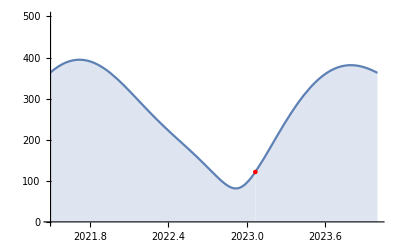

```mathematica
distanceEarthToMars[year_?NumericQ]:=AstroDistance[
Entity["Planet","Mars"],{Entity["Planet","Earth"],DateObject[{year},CalendarType->"GregorianYear"]}
]
Plot[distanceEarthToMars[year],
{year,2021.5,2024}, 
Filling->Bottom,
PlotRange->{0,500},
TargetUnits->"Gigameters",
Exclusions->{year == DateObject[CalendarType->"GregorianYear"]["DateList"][[1]]},
ExclusionsStyle->{AbsolutePointSize[10],Red}]
```

Closest distance in that timespan:

```mathematica
FindMinimum[QuantityMagnitude[distanceEarthToMars[year]],{year,2022,2024}]
```

{0.544465,{year→2022.92}}

Draw the position of Mars in that timespan, on the galactic sky backdrop, using the equatorial reference frame.

```mathematica
marsPosition=AstroPosition[
Entity["Planet","Mars"],
{"Equatorial", #}]&/@DateRange["1 July 2021","31 December 2023", Quantity[10,"Day"]];
AstroGraphics[{White,Point[marsPosition]},
AstroReferenceFrame-> {"Equatorial"},
AstroBackground->"GalacticSky"]
```

-Graphics-

Bonus: plot the movement of Mars and Earth in that time frame:

```mathematica
Manipulate[
ResourceFunction["SolarSystemPlot3D"][{
LightBlue,EdgeForm[],Sphere[Entity["Planet","Earth"], .05],
Orange,EdgeForm[], Sphere[Entity["Planet","Mars"],.05]},
date,
Boxed -> False,
"SunStyle"->{Yellow,EdgeForm[], Lighting->{{"Ambient",GrayLevel[.3]},{"Directional",White,ImageScaled[{0,0,1}]}},Sphere[{0,0,0},.1]},
Background->Black,
"OrbitStyle"->Gray,
LabelStyle -> Orange,
"IncludeReferenceObjects"->False,
LabelingFunction->Callout],{
date,DateObject[{2021,07,01}],DateObject[{2023,12,31}],Quantity[10,"Days"]}]
```